```mathematica
Quit[]
```

NFW OF LMC. Density profiles and compute D-factors (without cheese-mask. Just to have an approximate value).
 https://www.aanda.org/articles/aa/pdf/2024/12/aa51578-24.pdf also contains the coordinates of the LMC (dynamical) center

```mathematica
SolarMass=1.988 10^(30);(*Kg*)
eVtoKg=1.782662×10^(-36) ;(*Kg*)
pc=3.0857 10^(16) ;(*in m*)
(*NFW from MR paper https://arxiv.org/pdf/2106.08025*)
rs=9.8;(*kpc*)
ρs=5.1 10^6  SolarMass 1/eVtoKg 10^(-9) (10^3 pc 10^2)^(-3) (*GeV cm-3*)
NFW[r_]:=ρs rs/r (1+r/rs)^(-2);
(*NFW from https://www.aanda.org/articles/aa/pdf/2024/12/aa51578-24.pdf
I use second column from Table1
*)
rs2=10^(4.30) 10^(-3);(*kpc*)
ρs2=10^(-2.47) 10^9 SolarMass 1/eVtoKg 10^(-9) (10^3 pc 10^2)^(-3); (*GeV cm-3*)
NFW2[r_]:=ρs2 rs2/r (1+r/rs2)^(-2);
(*NFW from https://www.aanda.org/articles/aa/pdf/2024/12/aa51578-24.pdf
I use first column from Table1
*)
rs3=10^(4.02) 10^(-3);(*kpc*)
ρs3=10^(-1.99) 10^9 SolarMass 1/eVtoKg 10^(-9) (10^3 pc 10^2)^(-3); (*GeV cm-3*)
NFW3[r_]:=ρs3 rs3/r (1+r/rs3)^(-2);
(*From https://arxiv.org/pdf/2509.13540
From Fig.1: profile valid up to 4-5 kpc, which corresponds to 4.5 -5.7 deg from the center.
*)
(*
The center of LMC they take is l=79.5◦,b=−32.9◦
which should be ...
*)
αE=0.277;
rE=5.65;
ρE=9.36 10^6SolarMass 1/eVtoKg 10^(-9) (10^3 pc 10^2)^(-3) (*GeV cm-3*);
Einasto[r_]:=ρE Exp[-2/αE ((r/rE)^αE-1)]
NFW[50]
```

0.193578

0.00101897

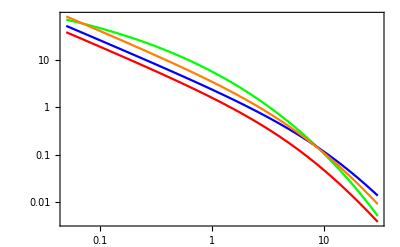

```mathematica
LogLogPlot[{Einasto[r],NFW[r],NFW2[r],NFW3[r]},{r,0.05,30},Frame->True,PlotStyle->{Green,Red,Blue,Orange}]
```

```mathematica
(*Integral until R200 to check that I obtain M200 in Table 1 of https://www.aanda.org/articles/aa/pdf/2024/12/aa51578-24.pdf*)
```

```mathematica
NIntegrate[4 Pi r^2NFW2[r],{r,0,156}] (SolarMass 1/eVtoKg 10^(-9) (10^3 pc 10^2)^(-3))^(-1)
NIntegrate[4 Pi r^2NFW3[r],{r,0,75}] (SolarMass 1/eVtoKg 10^(-9) (10^3 pc 10^2)^(-3))^(-1)
```

4.364×10^11

1.80427×10^11

```mathematica
pc=3.0857 10^(16) ;(*in m*)
Kpc=10^3 pc;(*pc*)
d=50.;(*kpc*)
Profile[r_]:=NFW[r]
RGCθ[s_,θ_]:=Module[{x,y,z},z=s Sin[θ];y=0;x=d-s Cos[θ];Sqrt[x^2+y^2+z^2]]
step=1.;
LosDθ[θ_]:=(Kpc 10^2)(NIntegrate[Profile[RGCθ[s,θ]],{s,0.,d-step}]+NIntegrate[Profile[RGCθ[s,θ]],{s,d-step,d+step},Method->{Automatic,"SymbolicProcessing" -> 0}]+NIntegrate[Profile[RGCθ[s,θ]],{s,d+step,1.5d}])
```

InterpolatingFunction[…]

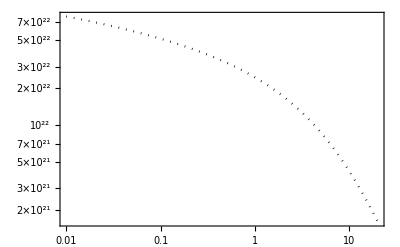

```mathematica
Npoints=300;
θmin=0.01;
θmax=20.;
Do[aθ[i]=10^(Log10[θmin]+Log10[θmax/θmin]*i/Npoints) Pi/180;(*rad*)
aIntelosθ[i]=LosDθ[aθ[i]],{i,0,Npoints}]
dDdΩθLogLog=Interpolation[Table[{Log10@aθ[i],Log10@aIntelosθ[i]},{i,0,Npoints}],InterpolationOrder->1]
dDdΩ[x_]:=10^(dDdΩθLogLog[Log10[x]])
dDdΩ[x_]:=10.^(dDdΩθLogLog[Log10[x]])
LogLogPlot[{dDdΩ[α Pi/180]},{α,θmin ,θmax},Frame->True,PlotStyle->{Darker[Green],{Black,Dotted}}(*,FrameLabel->{StyleFrameLabel["θ [rad]"],StyleFrameLabel["dD/dΩ(α) [GeV cm^-2sr^-1]"]},
FrameStyle-> StyleFrameTicks*)
]
```

```mathematica
αint=5.0;
ΔΩ=2Pi(1-Cos[αint Pi/180]);
Dfact=2Pi NIntegrate[Sin[α]dDdΩ[α ],{α, θmin Pi/180., αint Pi/180}];
Print["D GeV cm-2 ",Dfact," for θ [deg] ",αint," D/ΔΩ GeV cm-2 sr-1 ",Dfact/ΔΩ]
```

```mathematica
(*NFW*)
```

D GeV cm-2 3.17419×10^20 for θ [deg] 5. D/ΔΩ GeV cm-2 sr-1 1.32759×10^22

```mathematica
(*NFW2*)
```

D GeV cm-2 8.26177×10^20 for θ [deg] 6. D/ΔΩ GeV cm-2 sr-1 2.40029×10^22

```mathematica
(*NFW*)
```

D GeV cm-2 4.00704×10^20 for θ [deg] 6. D/ΔΩ GeV cm-2 sr-1 1.16416×10^22

```mathematica
(*NFW*)
```

D GeV cm-2 7.28479×10^20 for θ [deg] 10. D/ΔΩ GeV cm-2 sr-1 7.63159×10^21

```mathematica
(*NFW2*)
```

D GeV cm-2 1.64505×10^21 for θ [deg] 10. D/ΔΩ GeV cm-2 sr-1 1.72336×10^22

```mathematica
(*NFW2*)
```

D GeV cm-2 6.35722×10^20 for θ [deg] 5. D/ΔΩ GeV cm-2 sr-1 2.65888×10^22

```mathematica
(*NFW3*)
```

D GeV cm-2 3.51224×10^20 for θ [deg] 3.

```mathematica
(*NFW2*)
```

D GeV cm-2 2.93981×10^20 for θ [deg] 3. D/ΔΩ GeV cm-2 sr-1 3.41406×10^22

```mathematica
(*Einasto*)
```

D GeV cm-2 4.69476×10^20 for θ [deg] 3.

```mathematica
(*NFW*)
```

D GeV cm-2 1.57511×10^20 for θ [deg] 3. D/ΔΩ GeV cm-2 sr-1 1.82921×10^22

```mathematica
(*NFW*)
```

D GeV cm-2 5.55238×10^19 for θ [deg] 1.5